# Prakhar Khugshal | BSC(hons) CS | 20211441 | IV semester

## Newton Raphson Method

## Q1

x0=1

Nmax=2

epsilon=10

f[x]:=Cos[x]

f'[x]:=-Sin[x]

Return[1.64209]

The final approximationof the root is :1.64209

estimated error is :0.642093

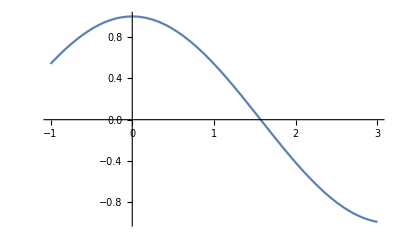

```mathematica
x0 = Input["Enter first guess: "];
Nmax = Input["Enter maximum of iterations : " ];
eps= Input["Enter the value of covergence parameter: "];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x];
Print["f[x]:=",f[x]]
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤ Nmax,i++,x1=N[x0-(f[x]/.x-> x0)/(D[f[x],x]/.x-> x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"Th number of iteration the root is :",x1];Print["estimated error is:",Abs[x1-x0p]]];
Print["The final approximationof the root is :",x1];
Print["estimated error is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

## Q2

x0=1

Nmax=20

epsilon=1/1000000

f[x]:=1-5 x+x^3

f'[x]:=-5+3 x^2

In1Th number of iteration the root is :-0.5

estimated error is:1.5

In2Th number of iteration the root is :0.294118

estimated error is:0.794118

In3Th number of iteration the root is :0.200215

estimated error is:0.093903

In4Th number of iteration the root is :0.201639

estimated error is:0.00142474

Return[0.20164]

The final approximationof the root is :0.20164

estimated error is :2.50538×10^-7

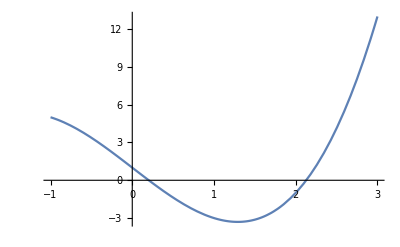

```mathematica
x0 = Input["Enter first guess: "];
Nmax = Input["Enter maximum of iterations : " ];
eps= Input["Enter the value of covergence parameter: "];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=x^3-5*x+1;
Print["f[x]:=",f[x]]
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤ Nmax,i++,x1=N[x0-(f[x]/.x-> x0)/(D[f[x],x]/.x-> x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"Th number of iteration the root is :",x1];Print["estimated error is:",Abs[x1-x0p]]];
Print["The final approximationof the root is :",x1];
Print["estimated error is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

## Q3

x0=1

Nmax=20

epsilon=1.×10^-6

f[x]:=-ⅇ^x x+Cos[x]

f'[x]:=-ⅇ^x-ⅇ^x x-Sin[x]

In1Th number of iteration the root is :0.653079

estimated error is:0.346921

In2Th number of iteration the root is :0.531343

estimated error is:0.121736

In3Th number of iteration the root is :0.51791

estimated error is:0.0134335

In4Th number of iteration the root is :0.517757

estimated error is:0.00015253

Return[0.517757]

The final approximationof the root is :0.517757

estimated error is :1.94824×10^-8

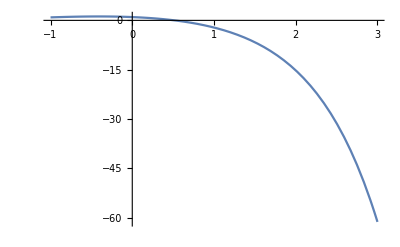

```mathematica
x0 = Input["Enter first guess: "];
Nmax = Input["Enter maximum of iterations : " ];
eps= Input["Enter the value of covergence parameter: "];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x]-x*Exp[x];
Print["f[x]:=",f[x]]
Print["f'[x]:=",D[f[x],x]];
For[i=1,i≤ Nmax,i++,x1=N[x0-(f[x]/.x-> x0)/(D[f[x],x]/.x-> x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"Th number of iteration the root is :",x1];Print["estimated error is:",Abs[x1-x0p]]];
Print["The final approximationof the root is :",x1];
Print["estimated error is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```